```mathematica
eegYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGyes_signal.mat"];
numSamplesEegYes = Dimensions[eegYesMatlab][[3]];
eegYesRaw =  Table[Transpose[eegYesMatlab[[1,1,x]]],{x,numSamplesEegYes}];

eegNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/EEGno_signal.mat"];
numSamplesEegNo = Dimensions[eegNoMatlab][[3]];
eegNoRaw =  Table[Transpose[eegNoMatlab[[1,1,x]]],{x,numSamplesEegNo}];

eegDataFullYes = Table[eegYesRaw[[x,All,All]]-> "Yes",{x,numSamplesEegYes}];
eegDataFullNo = Table[eegNoRaw[[x,All,All]]-> "No",{x,numSamplesEegNo}];

eegFullDataYesAndNo = Join[eegDataFullYes,eegDataFullNo];
```

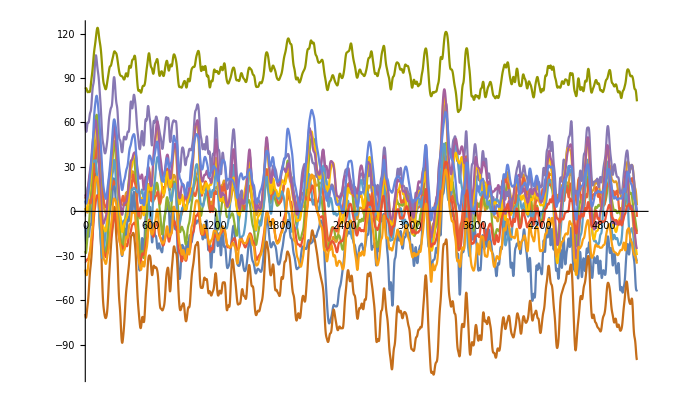

```mathematica
ListLinePlot[eegYesRaw[[2]]]
```

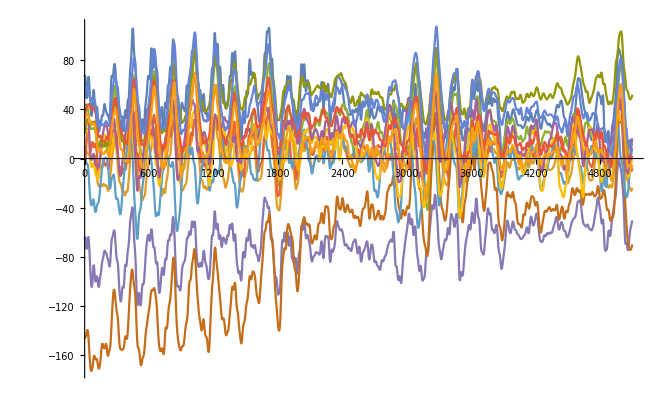

```mathematica
ListLinePlot[eegNoRaw[[3]]]
```

```mathematica
Dimensions[eegNoRaw]
```

{30,13}

```mathematica
redTest = DimensionReduce[Transpose@eegNoRaw[[1]],3, Method->"PrincipalComponentsAnalysis"]
```

{{4.32106,-0.299704,2.38526},{4.24501,-0.317635,2.44193},5098,{-1.87815,-2.3159,-1.29526},{-1.82292,-2.27911,-1.32257}}
 |  |  |  |

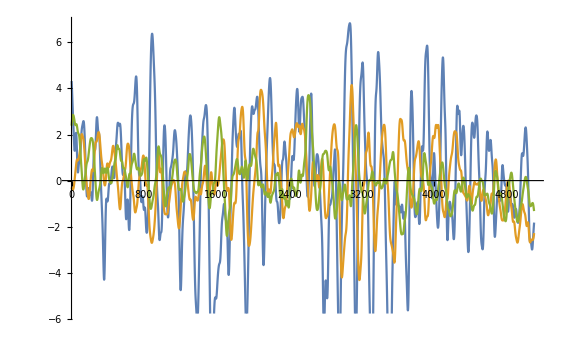

```mathematica
ListLinePlot[Transpose@redTest]
```

```mathematica
ListLinePlot@Square@Abs@Fourier@Transpose@redTest
```

ListLinePlot::lpn: □{{3.63144×10^-13,8.12538,15.8745,32.7666,8.42113,14.8687,3.00513,13.7488,«35»,3.16824,0.914155,4.07427,10.1892,5.52377,3.56356,4.37756,«5052»},{«1»},{«24»,«50»}} is not a list of numbers or pairs of numbers.

ListLinePlot[□{1}]
 |  |  |  |

```mathematica
Square[x]
```

□x